```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/sec_int_data/862nm.dat"]
```

{{1.63065,-0.15711},{1.58758,-0.175294},{1.51023,-0.174246},{1.46132,-0.172486},{1.41705,-0.159218},{1.38078,-0.15059},{1.34407,-0.136759},{1.30453,-0.168123},{1.27782,-0.149266},{1.24828,-0.155228},{1.22646,-0.136954},{1.20042,-0.137516},{1.183,-0.151474},{1.16401,-0.136278},{1.14739,-0.145049},{1.13423,-0.159136},{1.12389,-0.17251},{1.11401,-0.452069},{1.10574,-0.349799},{1.09905,-0.52251},{1.09389,-0.524756},{1.08918,-0.256429},{1.08895,-0.263627},{1.08874,-0.215436},{1.08738,-0.111267},{1.08767,-0.118738},{1.08994,-0.127493},{1.0948,-0.127595},{1.10288,-0.121377},{1.1168,-0.122767},{1.12832,-0.142532},{1.1517,-0.115209},{1.18117,-0.100948},{1.20042,-0.136679},{1.25083,-0.128333},{1.28067,-0.123955},{1.3108,-0.113023},{1.33715,-0.134332}}

-0.400761+0.178348 x

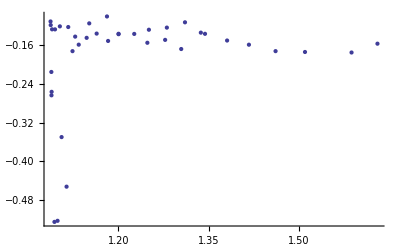

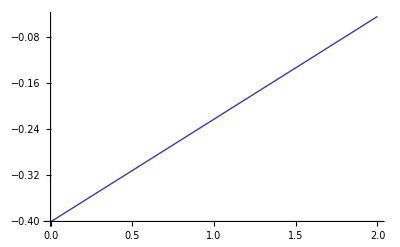

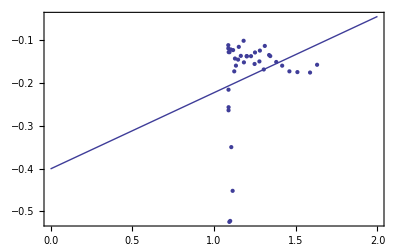

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```